# Fisher estimates for a power law mass spectrum

```mathematica
SetDirectory@NotebookDirectory[];
<<MaTeX`
```

## No selection effects

## Inputs

```mathematica
$Assumptions={θ>0,θmax>0,θmin>0,θmax>θmin, σ>0 & σ<1000,λ>-1}
```

{θ>0,θmax>0,θmin>0,θmax>θmin,σ (σ>0&)<1000,λ>-1}

In this first example we do not consider selection effects, meaning we set the probability of detection for both source and population parameters to one.

```mathematica
pdetθ[M_]:=1
pdetλ[λ_]:=1
ppop[{θ_,θmin_,θmax_},λ_]:= λ/(θmax^λ-θmin^λ) θ^(λ-1)
```

We check here that the population model is correctly normalized.

```mathematica
Integrate[ppop[{θ,θmin,θmax},λ],{θ,θmin,θmax}]
```

1

A bunch of useful quantities that enter the Fisher matrix.

```mathematica
Γ = 1/σ^2;  (* True only in the case in which d = θ + noise. *)
Dmij= Γ ;  (* Only true in the absence of selection effects. *)
Dmi = D[pdetθ[θ],θ];
P = D[Log@ppop[{θ,θmin,θmax},λ],θ];
H = - D[D[Log@ppop[{θ,θmin,θmax},λ],θ],θ];
```

Choose the true parameters here.

```mathematica
λtrue =0.00001;
truepars ={Nobs->1000,λ->λtrue,σ->0.1,θmax->10^7, θmin->10^4}//N;
```

## Fisher matrix and precision estimates [only retaining first term]

In this simplified scenario, we only consider the first (dominant) contribution to the Fisher matrix, without considering selection effects.
Notice that M is integrated out in the interval 10^4 M_0< M < 10^7 M_0.

```mathematica
SimpPopFisherNoSelectionEffects[λ_,{θ_,θmin_,θmax_},{i_,j_}]:=
Integrate[(1/ppop[{θ,θmin,θmax},λ])D[ppop[{θ,θmin,θmax},λ],i]*D[ppop[{θ,θmin,θmax},λ],j],{θ,θmin,θmax}]
```

```mathematica
ΓλλSimpNoSelectionEffects = SimpPopFisherNoSelectionEffects[λ,{M,Mmin,Mmax},{λ,λ}];//Timing
```

{224.657,Null}

```mathematica
√(1/(Nobs*ΓλλSimpNoSelectionEffects))
Δα =%/.{Mmax->θmax, Mmin->θmin}/.truepars
```

√(1/(Nobs (1/λ^2-(Mmax^λ Mmin^λ (Log[Mmax]-Log[Mmin])^2)/((Mmax^λ-Mmin^λ)^2))))

0.0157423

```mathematica
√(1/(Nobs*ΓλλSimpNoSelectionEffects))//InputForm (*to simpify in Python. *)
```

Sqrt[1/(Nobs*(λ^(-2) - (Mmax^λ*Mmin^λ*(Log[Mmax] - Log[Mmin])^2)/(Mmax^λ - Mmin^λ)^2))]

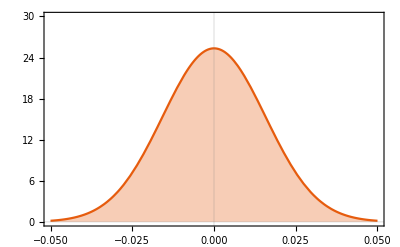

```mathematica
SimplifiedFisher=Plot[
PDF[NormalDistribution[λtrue,Δα],x]//Evaluate,{x,-.05,.05},
Filling->Axis,PlotRange->{All,{0,30}},
FrameLabel->{{MaTeX["\\text{PDF}",FontSize->17],None},{MaTeX["\\alpha_0",FontSize->17],None}},
FrameTicksStyle->Directive[Black,13],
TicksStyle->Directive[Black,AbsoluteThickness[100]],
PlotTheme-> "Scientific", 
Frame->True]
```

## Fisher matrix and precision estimates [including all terms]

Notice that M is integrated out in the interval 10^4 M_0< M < 10^7 M_0.

```mathematica
Γλλ=With[{θmin =10^4 ,θmax = 10^7,Γ = Γ, H = H, D2 = Dmij,D1=Dmi},
model = ppop[{θ,θmin,θmax},λ];
a = Integrate[(pdetθ[θ]/(model pdetλ[λ]))D[model,λ]*D[model,λ],{θ,θmin,θmax}];
b = - 1/pdetλ[λ]^2 D[pdetλ[λ],λ]*D[pdetλ[λ],λ];
c = 1/2 Integrate[D[D[Log@(Γ+H),λ],λ] pdetθ[θ]/pdetλ[λ] model,{θ,θmin,θmax}];
d =-1/2 Integrate[D[D[(Γ+H)^-1,λ],λ]D2 model/pdetλ[λ],{θ,θmin,θmax}];
e =- Integrate[D[D[P(Γ+H)^-1,λ],λ]D1 model/pdetλ[λ],{θ,θmin,θmax}];
f = -Integrate[D[D[P^2(Γ+H)^-1,λ],λ] model/pdetλ[λ],{θ,θmin,θmax}];
a+b+c+d+e+f
];//Timing
```

{70.7151,Null}

```mathematica
√(1/(Nobs*Γλλ));
%/.truepars
Δαfull=Re[%]
```

0.0158814+8.87709×10^-10 ⅈ

0.0158814

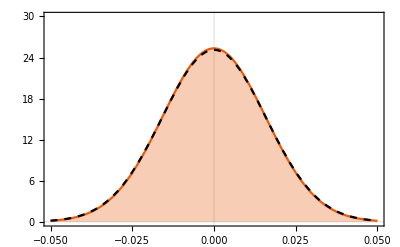

```mathematica
FullFisher = Plot[PDF[NormalDistribution[λtrue,Δαfull],x]//Evaluate,{x,-.05,.05},PlotStyle->{Black,Dashed}];
Show[SimplifiedFisher,FullFisher]
```

## Helpful expressions for the case with selection effects

## Inputs

The aim here is not to calculate the expression analytically, as it would be too hard to do. 
We instead help the numerical integration in Python by obtaining some analytical expressions that are valid for the specific case of a power law distribution.

```mathematica
$Assumptions={σ>0};
```

```mathematica
σθ=1/2 Erfc[(dth-θ)/(√2 √(σ^2))]; 
pθλ = ppop[{θ,θmin,θmax},λ];
```

```mathematica
Dm1 = D[σθ,θ];
Dm2 = Γ;
Hij=-D[D[pθλ,θ],θ];
Pj = D[Log@pθλ,θ];
```

```mathematica
somepars={θmin->10^4,θmax->10^7};
```

The FM expression can be written as int of function of θ times p(θ|λ), integrated over θ, which can be treated with Monte Carlo methods by drawing samples from p(θ|λ) and using them as input for the function of θ. Below are the expressions needed for such a function of θ.

## Expressions for the first term (dominant for small noise variances)

The first term of the Fisher matrix (as in the master equation of the paper) is of the form

```mathematica
Framed[-D[D[Log[ppopmodel[λ]/pλ[λ]],λ],λ]//FullSimplify]
```

(ppopmodel'[λ]^2-ppopmodel[λ] ppopmodel''[λ])/ppopmodel[λ]^2+(-pλ'[λ]^2+pλ[λ] pλ''[λ])/pλ[λ]^2

where ppopmodel stands for the population model, and derivatives are with respect λ. The function above necessitates expressions for the derivatives of ppopmodel up to second order, which for the model we are considering read

```mathematica
D[pθλ,λ]/.{θ->Exp[θ] }//Simplify
```

1/((θmax^λ-θmin^λ)^2)(ⅇ^θ)^(-1+λ) (θmax^λ-θmin^λ+(θmax^λ-θmin^λ) λ Log[ⅇ^θ]-θmax^λ λ Log[θmax]+θmin^λ λ Log[θmin])

```mathematica
D[D[pθλ,λ],λ]/.{θ->Exp[θ]}//Simplify
```

1/((θmax^λ-θmin^λ)^3)(ⅇ^θ)^(-1+λ) ((θmax^λ-θmin^λ)^2 λ Log[ⅇ^θ]^2+θmax^λ (θmax^λ+θmin^λ) λ Log[θmax]^2-2 (θmax^λ-θmin^λ) Log[ⅇ^θ] (-θmax^λ+θmin^λ+θmax^λ λ Log[θmax]-θmin^λ λ Log[θmin])-2 θmax^λ Log[θmax] (θmax^λ-θmin^λ+2 θmin^λ λ Log[θmin])+θmin^λ Log[θmin] (2 (θmax^λ-θmin^λ)+(θmax^λ+θmin^λ) λ Log[θmin]))

These expressions have been coded up in the accompanying Python notebook.

Notice:  the notebook here takes input θ=M, whereas the Python notebook takes θ=lnM as parameter. As a result in all the expressions in this section we translate the parameter to  θ=lnM to avoid miscommunication with the Python notebook.

The first term of the Fisher matrix also depends on the derivatives of the selection function, which in the Python notebook’s markdowns are related to the first and second derivative of the population model. Therefore all we need for the Monte Carlo integrals in the Python notebooks are the expressions below.

```mathematica
D[Log[pθλ],λ]//Simplify
```

1/((θmax^λ-θmin^λ) λ)(θmax^λ-θmin^λ+(θmax^λ-θmin^λ) λ Log[θ]-θmax^λ λ Log[θmax]+θmin^λ λ Log[θmin])

```mathematica
D[D[Log[pθλ],λ],λ]//Simplify
```

1/((θmax^λ-θmin^λ)^2 λ^2)(-(θmax^λ-θmin^λ)^2+θmax^λ θmin^λ λ^2 Log[θmax]^2-2 θmax^λ θmin^λ λ^2 Log[θmax] Log[θmin]+θmax^λ θmin^λ λ^2 Log[θmin]^2)

## Expressions for the other terms (subdominant for small noise variances)

The second term in the Fisher matrix depends on a double derivative of the form

```mathematica
Framed[D[D[Log[F[λ]],λ],λ]//Simplify]
```

(-F'[λ]^2+F[λ] F''[λ])/F[λ]^2

where F(λ) = Γ+H_ij(λ) here. Therefore, we need to evaluate

```mathematica
Γ + Hij/.{θ->Exp[θ]}//FullSimplify
```

(ⅇ^(θ (-3+λ)) (-2+λ) (-1+λ) λ)/(-θmax^λ+θmin^λ)+1/σ^2

```mathematica
D[Γ + Hij,λ]/.{θ->Exp[θ]}//FullSimplify
```

(ⅇ^(θ (-3+λ)) (-((θmax^λ-θmin^λ) (2+(3+θ (-1+λ)) (-2+λ) λ))+(-2+λ) (-1+λ) λ (θmax^λ Log[θmax]-θmin^λ Log[θmin])))/((θmax^λ-θmin^λ)^2)

```mathematica
D[D[Γ + Hij,λ],λ]/.{θ->Exp[θ]}//FullSimplify
```

1/((θmax^λ-θmin^λ)^3)ⅇ^(θ (-3+λ)) (-((θmax^(2 λ)+θmin^(2 λ)-2 (θmax θmin)^λ) (6 (-1+λ)+θ (4+(6+θ (-1+λ)) (-2+λ) λ)))-θmax^λ (θmax^λ+θmin^λ) (-2+λ) (-1+λ) λ Log[θmax]^2+2 (θmin^(2 λ)-(θmax θmin)^λ) (2+(3+θ (-1+λ)) (-2+λ) λ) Log[θmin]-(θmin^(2 λ)+(θmax θmin)^λ) (-2+λ) (-1+λ) λ Log[θmin]^2+2 θmax^λ Log[θmax] ((θmax^λ-θmin^λ) (2+(3+θ (-1+λ)) (-2+λ) λ)+2 θmin^λ (-2+λ) (-1+λ) λ Log[θmin]))

The third term in the Fisher matrix depends on the following term

```mathematica
-1/2 D[D[(Γ + Hij)^-1,λ],λ]Dm2/.{θ->Exp[θ]}//Simplify
```

-((ⅇ^(3 θ) (ⅇ^θ)^(2 λ) σ^4 (2 θmax^λ-2 θmin^λ-6 θmax^λ λ+6 θmin^λ λ+3 θmax^λ λ^2-3 θmin^λ λ^2+(θmax^λ-θmin^λ) λ (2-3 λ+λ^2) Log[ⅇ^θ]-θmax^λ λ (2-3 λ+λ^2) Log[θmax]+2 θmin^λ λ Log[θmin]-3 θmin^λ λ^2 Log[θmin]+θmin^λ λ^3 Log[θmin])^2)/((θmax^λ-θmin^λ) (ⅇ^(3 θ) (θmax^λ-θmin^λ)-(ⅇ^θ)^λ λ (2-3 λ+λ^2) σ^2)^3))+(ⅇ^(-3 θ) (ⅇ^θ)^λ (-2 (θmax^λ-θmin^λ)^2 (-2+λ)-2 (θmax^λ-θmin^λ)^2 (-1+λ)-2 (θmax^λ-θmin^λ)^2 λ-2 (θmax^λ-θmin^λ)^2 (-2+λ) (-1+λ) Log[ⅇ^θ]-2 (θmax^λ-θmin^λ)^2 (-2+λ) λ Log[ⅇ^θ]-2 (θmax^λ-θmin^λ)^2 (-1+λ) λ Log[ⅇ^θ]-(θmax^λ-θmin^λ)^2 (-2+λ) (-1+λ) λ Log[ⅇ^θ]^2+2 (θmax^λ-θmin^λ) (-2+λ) (-1+λ) (θmax^λ Log[θmax]-θmin^λ Log[θmin])+2 (θmax^λ-θmin^λ) (-2+λ) λ (θmax^λ Log[θmax]-θmin^λ Log[θmin])+2 (θmax^λ-θmin^λ) (-1+λ) λ (θmax^λ Log[θmax]-θmin^λ Log[θmin])+2 (θmax^λ-θmin^λ) (-2+λ) (-1+λ) λ Log[ⅇ^θ] (θmax^λ Log[θmax]-θmin^λ Log[θmin])-2 (-2+λ) (-1+λ) λ (θmax^λ Log[θmax]-θmin^λ Log[θmin])^2+(θmax^λ-θmin^λ) (-2+λ) (-1+λ) λ (θmax^λ Log[θmax]^2-θmin^λ Log[θmin]^2)))/(2 (θmax^λ-θmin^λ)^3 (1/σ-((ⅇ^θ)^(-3+λ) (-2+λ) (-1+λ) λ σ)/(θmax^λ-θmin^λ))^2)

the fourth on

```mathematica
-D[D[Pj(Γ + Hij)^-1,λ],λ]Dm1/.{θ->Exp[θ]}//Simplify
```

(ⅇ^(-7 θ-((dth-ⅇ^θ)^2)/(2 σ^2)) (ⅇ^θ)^λ σ^3 (2 (θmax^λ-θmin^λ) (ⅇ^(3 θ) (-θmax^λ+θmin^λ)+(ⅇ^θ)^λ λ (2-3 λ+λ^2) σ^2) (2 θmax^λ-2 θmin^λ-6 θmax^λ λ+6 θmin^λ λ+3 θmax^λ λ^2-3 θmin^λ λ^2+(θmax^λ-θmin^λ) λ (2-3 λ+λ^2) Log[ⅇ^θ]-θmax^λ λ (2-3 λ+λ^2) Log[θmax]+2 θmin^λ λ Log[θmin]-3 θmin^λ λ^2 Log[θmin]+θmin^λ λ^3 Log[θmin])-2 (ⅇ^θ)^λ (-1+λ) σ^2 (2 θmax^λ-2 θmin^λ-6 θmax^λ λ+6 θmin^λ λ+3 θmax^λ λ^2-3 θmin^λ λ^2+(θmax^λ-θmin^λ) λ (2-3 λ+λ^2) Log[ⅇ^θ]-θmax^λ λ (2-3 λ+λ^2) Log[θmax]+2 θmin^λ λ Log[θmin]-3 θmin^λ λ^2 Log[θmin]+θmin^λ λ^3 Log[θmin])^2-ⅇ^(3 θ) (1-λ) (θmax^λ-θmin^λ-ⅇ^(-3 θ) (ⅇ^θ)^λ (-2+λ) (-1+λ) λ σ^2) (-2 (θmax^λ-θmin^λ)^2 (-2+λ)-2 (θmax^λ-θmin^λ)^2 (-1+λ)-2 (θmax^λ-θmin^λ)^2 λ-2 (θmax^λ-θmin^λ)^2 (-2+λ) (-1+λ) Log[ⅇ^θ]-2 (θmax^λ-θmin^λ)^2 (-2+λ) λ Log[ⅇ^θ]-2 (θmax^λ-θmin^λ)^2 (-1+λ) λ Log[ⅇ^θ]-(θmax^λ-θmin^λ)^2 (-2+λ) (-1+λ) λ Log[ⅇ^θ]^2+2 (θmax^λ-θmin^λ) (-2+λ) (-1+λ) (θmax^λ Log[θmax]-θmin^λ Log[θmin])+2 (θmax^λ-θmin^λ) (-2+λ) λ (θmax^λ Log[θmax]-θmin^λ Log[θmin])+2 (θmax^λ-θmin^λ) (-1+λ) λ (θmax^λ Log[θmax]-θmin^λ Log[θmin])+2 (θmax^λ-θmin^λ) (-2+λ) (-1+λ) λ Log[ⅇ^θ] (θmax^λ Log[θmax]-θmin^λ Log[θmin])-2 (-2+λ) (-1+λ) λ (θmax^λ Log[θmax]-θmin^λ Log[θmin])^2+(θmax^λ-θmin^λ) (-2+λ) (-1+λ) λ (θmax^λ Log[θmax]^2-θmin^λ Log[θmin]^2))))/(√(2 π) (θmax^λ-θmin^λ) (θmax^λ-θmin^λ-ⅇ^(-3 θ) (ⅇ^θ)^λ (-2+λ) (-1+λ) λ σ^2)^3)

and finally the fifth on

```mathematica
-1/2 D[D[Pj^2(Γ + Hij)^-1,λ],λ]Dm2/.{θ->Exp[θ]}//Simplify
```

-1/(2 σ^2)((2 ⅇ^(-2 θ))/(-((ⅇ^θ)^(-3+λ) (-2+λ) (-1+λ) λ)/(θmax^λ-θmin^λ)+1/σ^2)+(4 (ⅇ^θ)^(1+λ) (-1+λ) σ^4 (2 θmax^λ-2 θmin^λ-6 θmax^λ λ+6 θmin^λ λ+3 θmax^λ λ^2-3 θmin^λ λ^2+(θmax^λ-θmin^λ) λ (2-3 λ+λ^2) Log[ⅇ^θ]-θmax^λ λ (2-3 λ+λ^2) Log[θmax]+2 θmin^λ λ Log[θmin]-3 θmin^λ λ^2 Log[θmin]+θmin^λ λ^3 Log[θmin]))/(ⅇ^(3 θ) (θmax^λ-θmin^λ)-(ⅇ^θ)^λ λ (2-3 λ+λ^2) σ^2)^2+(2 (ⅇ^θ)^(1+2 λ) (-1+λ)^2 σ^6 (2 θmax^λ-2 θmin^λ-6 θmax^λ λ+6 θmin^λ λ+3 θmax^λ λ^2-3 θmin^λ λ^2+(θmax^λ-θmin^λ) λ (2-3 λ+λ^2) Log[ⅇ^θ]-θmax^λ λ (2-3 λ+λ^2) Log[θmax]+2 θmin^λ λ Log[θmin]-3 θmin^λ λ^2 Log[θmin]+θmin^λ λ^3 Log[θmin])^2)/((θmax^λ-θmin^λ) (ⅇ^(3 θ) (θmax^λ-θmin^λ)-(ⅇ^θ)^λ λ (2-3 λ+λ^2) σ^2)^3)-(ⅇ^(-5 θ) (ⅇ^θ)^λ (-1+λ)^2 (-2 (θmax^λ-θmin^λ)^2 (-2+λ)-2 (θmax^λ-θmin^λ)^2 (-1+λ)-2 (θmax^λ-θmin^λ)^2 λ-2 (θmax^λ-θmin^λ)^2 (-2+λ) (-1+λ) Log[ⅇ^θ]-2 (θmax^λ-θmin^λ)^2 (-2+λ) λ Log[ⅇ^θ]-2 (θmax^λ-θmin^λ)^2 (-1+λ) λ Log[ⅇ^θ]-(θmax^λ-θmin^λ)^2 (-2+λ) (-1+λ) λ Log[ⅇ^θ]^2+2 (θmax^λ-θmin^λ) (-2+λ) (-1+λ) (θmax^λ Log[θmax]-θmin^λ Log[θmin])+2 (θmax^λ-θmin^λ) (-2+λ) λ (θmax^λ Log[θmax]-θmin^λ Log[θmin])+2 (θmax^λ-θmin^λ) (-1+λ) λ (θmax^λ Log[θmax]-θmin^λ Log[θmin])+2 (θmax^λ-θmin^λ) (-2+λ) (-1+λ) λ Log[ⅇ^θ] (θmax^λ Log[θmax]-θmin^λ Log[θmin])-2 (-2+λ) (-1+λ) λ (θmax^λ Log[θmax]-θmin^λ Log[θmin])^2+(θmax^λ-θmin^λ) (-2+λ) (-1+λ) λ (θmax^λ Log[θmax]^2-θmin^λ Log[θmin]^2)))/((θmax^λ-θmin^λ)^3 (-((ⅇ^θ)^(-3+λ) (-2+λ) (-1+λ) λ)/(θmax^λ-θmin^λ)+1/σ^2)^2))

Unfortunately for me, all of these terms have to be coded up in the Python notebook for the semi-analytic expressions we are looking for here.. sigh..